```mathematica
fruits={apples,oranges};
veggies={cucumbers,squash};
Join[fruits,veggies]
```

{apples,oranges,cucumbers,squash}

```mathematica
(* 列表的合并 *)

Sort[{apples,oranges,cucumbers,squash}]
```

{apples,cucumbers,oranges,squash}

```mathematica
squares
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
Sort[squares]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
(* Sort默认递增排序 *)
Sort[squares,Greater]
```

{100,81,64,49,36,25,16,9,4,1}

```mathematica
(* 递减排序 *)

(* a matrix is defined as a list of lists in mthmtc *)
data={{0,10},{1,25},{2,50}}
```

{{0,10},{1,25},{2,50}}

```mathematica
data//TableForm
```

0 | 10
1 | 25
2 | 50

```mathematica
(* lists都被认为是行向量 *)

data//MatrixForm
```

(0 | 10
1 | 25
2 | 50)

```mathematica
Transpose[data]
```

{{0,1,2},{10,25,50}}

```mathematica
Transpose[data]//MatrixForm
```

(0 | 1 | 2
10 | 25 | 50)

```mathematica
Clear[data]
```

```mathematica
data={{0,0.01},{1000,0.00625},{1800,0.00476},{2800,0.0037},{3600,0.00313},{4400,0.00270},{5200,0.00241},{6200,0.00208}}
```

{{0,0.01},{1000,0.00625},{1800,0.00476},{2800,0.0037},{3600,0.00313},{4400,0.0027},{5200,0.00241},{6200,0.00208}}

```mathematica
data//TableForm
```

0 | 0.01
1000 | 0.00625
1800 | 0.00476
2800 | 0.0037
3600 | 0.00313
4400 | 0.0027
5200 | 0.00241
6200 | 0.00208

```mathematica
TableForm[data,TableHeadings->{None,{"time in s","[A] in mol/L"}}]
```

```mathematica
{{"time in s", "[A] in mol/L"}, {0, 0.01}, {1000, 0.00625}, {1800, 0.00476}, {2800, 0.0037}, {3600, 0.00313}, {4400, 0.0027}, {5200, 0.00241}, {6200, 0.00208}}
(* TableHeadings->{行标题，列标题} *)
```

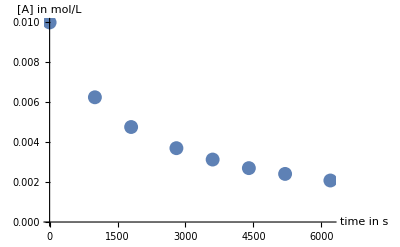

```mathematica
ListPlot[data,AxesLabel->{"time in s","[A] in mol/L"},PlotStyle->PointSize[0.025]]
```

```mathematica
(* 已知一级、二级反应的特征：
    1st order: Subscript[ln[A], t]=Subscript[ln[A], 0]-kt
2nd order: 1/[A]_t=1/[A]_0+kt
下面判断该反应的级数 *)
```

```mathematica
newdata=data;
newdata[[All,2]]=Log[data[[All,2]]];
(* [[All,2]]表示第2列 *)
newdata//TableForm
```

0 | -4.60517
1000 | -5.07517
1800 | -5.34751
2800 | -5.59942
3600 | -5.76672
4400 | -5.9145
5200 | -6.02813
6200 | -6.17539

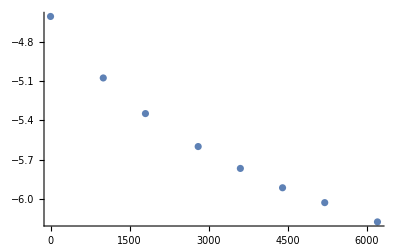

```mathematica
ListPlot[newdata]
```

```mathematica
newdata2=data;
newdata2[[All,2]]=1/data[[All,2]];
newdata2//TableForm
```

0 | 100.
1000 | 160.
1800 | 210.084
2800 | 270.27
3600 | 319.489
4400 | 370.37
5200 | 414.938
6200 | 480.769

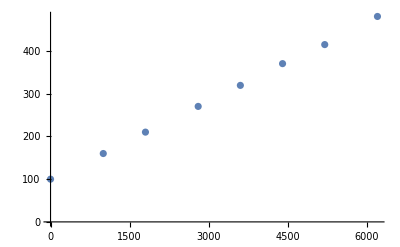

```mathematica
ListPlot[newdata2]
```